# Spin of a Fidget Spinner

Measuring the rotatin speed of a fidget spinner using sound.

Milad Pourrahmani (Miladiouss), Jun. 30,  2018

I was born in the early 1990s and I have witnessed the rise of the internet, smartphones, and social media. These inventions were surprising but not shocking. To me, it made sense why people would want to use the internet so they don’t have to go to a library, look at a screen so they don’t have to deal with reality, or socialize online so they have to face each other. But one thing that never made sense to me was the rise of fidit spinners. Just in case that you don’t know what spinner are, let me help you out.

Sometime in the April of 2017, suddenly everyone owned these spinning toys that served no purpose. It just didn't make sense. Why? To make the matter worse, these spinners were evolving. First, they were made of plastic and couldn't spin very long, Then they acquired LED lights. Slowly, they became these luxurious toys made entirely of high quality metals with fancy shapes and what not. As a full pledged hipster, I promised myself to avoid conformism and never buy one of these useless toys... despite the temptation!

Though I didn't purchase one myself, I soon became a spinner owner when a friend of mine gave me a very nice fidget spinner for Christmas. Little did they know what they have brought upon themselves! After playing spinning the spinner for a minute or two, feeling the gyroscopic effects, it was soon clear what I had to do. Measure how fast my spinner was spinning and quantify its decay rate.

## Measurements

Since the spinners are too fast for phone cameras to fully capture their motion, I decided to make my measurements using sound. I looked around, I found a wooden coffee mixer. Then, I gave my spinner a good push and approached the mixer such that it would have minimal contact with the spinner and I recorded the resulting sound using SystemDialogInput["RecordSound"].

```mathematica
audio=-Graphics-;
```

As it can be seen above, the amplitude varies between positive and negative values. One way to deal with that is to   corres the audio amplitude varies between positive and negative values. An easy way to normalize the data is by using the image function and for display purposes, we can partition this array to it would appear as a two dimensional image.

## Data Curation

First, import the audio and extract usable data from it :

```mathematica
(*audio = Sound[SampledSoundList[Abs@Flatten@ImageData@img,22050]]*)

audioDuration=Duration[audio];
audioSampleRate = AudioSampleRate[audio];
data = AudioData[audio][[1]];
data = Abs @ data;
```

## Detect Peaks in Audio

Second, use PeakDetect to see which points are peaks (= 1) and which points are not peaks (= 0). Find the location of peaks in seconds.

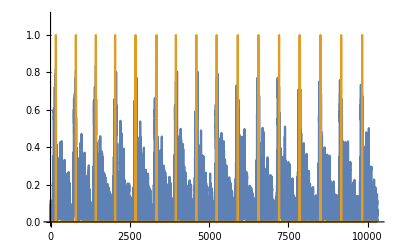

203

```mathematica
peaks=PeakDetect[data,150,0.0,0.4];
ListLinePlot[{data[[800;;11111]] ,PeakDetect[data[[800;;11111]],150,0.0,0.4]},PlotRange->{All,{0,1.1}}]
peakPos=1./audioSampleRate Position[peaks,1]//Flatten;
Length[peakPos]
```

## Spin Rate

The period of the spinner is the separation between the beats (peaks) times the number of blades:

```mathematica
periods = 6 (peakPos[[2;;-1]]-peakPos[[1;;-2]])/1;
```

Spin rate, that is revolutions per second, is reciprocal of the period:

```mathematica
spinRates=1/periods;(*Revolutions per second*)
```

Convert the data into a list of {time, spin rate} and plot it:

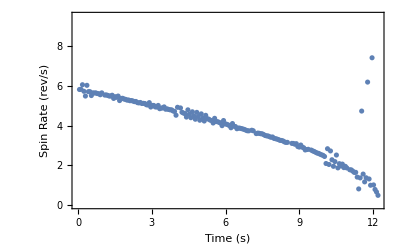

```mathematica
spinRateVStime=Table[{i audioDuration/Length[spinRates],spinRates[[i]]},{i,Length[spinRates]}];

ListPlot[spinRateVStime,Frame->True,FrameLabel->{"Time (s)","Spin Rate (rev/s)"}]
```

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

emailaddress@author.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)